# Delft’s Silicon device

reference: https://arxiv.org/abs/2202.09252
scientific contributors: Fernando, Simon

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

Load the QuESTLink

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Connectivity of this device

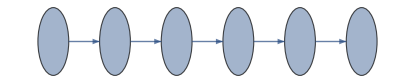

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->100,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* Natural frequencies of each qubit in MHz *)
Larmor-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(* The electromagnetic field in Tesla *)
BField->0.576,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
FreqSingleXY->5,
(* Error fraction/ratio {depolarising, dephasing} *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one
	the qubits represented below are the control ones *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
FidCZ-><|0->0.8961173996 ,1->0.903347176,2-> 0.8837068241 ,3->0.9582985365,4-> 0.9426960894|>,
(* Error fraction/ratio {depolarising, dephasing} *)
EFCZ->{0.2,0.8},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying two-qubit gates;square matrix with dims nqubit-2*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}
},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no two-qubit gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,
(* average of Rabi frequency (MHz) and fidelities of Controlled-Rotations around x- and y- axis. This gates are used in readout *)
FreqCRotXY->5,
FidCRotXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991|>
};
```

```mathematica
dev=SiliconDelft[];
```

```mathematica
InsertCircuitNoise[{Subscript[Rx, 0][2π],Subscript[Rz, 0][π],Subscript[Ry, 0][2π]},dev]
```

{{0,{Rx_0[2 π],Depol_0[0.],Deph_0[0.00345]},{}},{5,{Rz_0[π]},{}},{5,{Ry_0[2 π],Depol_0[0.],Deph_0[0.00345]},{}}}

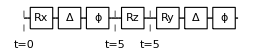

```mathematica
DrawCircuit[%]
```

```mathematica
<|0->5,1->5,2->5,3->5,4->5,5->5|>[0]
```

5

## Tests

Initialisation sequence
Measurement sequence
Obtain T2 epoch from the T2* 
Obtain Bell state preparation fidelity